```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls"
};
```

```mathematica
figureNameSensitivity ="Fig_SI_sensitivity_analysis";
```

```mathematica
sensitivityPars={αC,αP,αN,αU,βP,βN,ϕN,δN};
minSensitivityRange=0;
maxSensitivityRange=2;
```

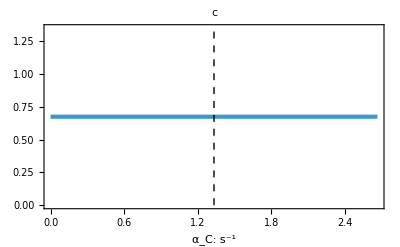
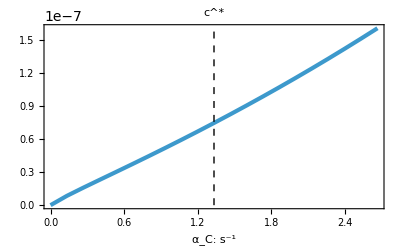
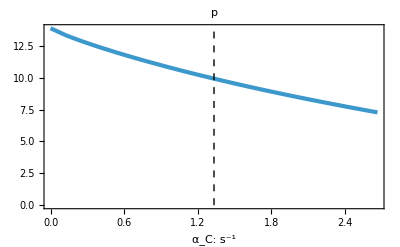
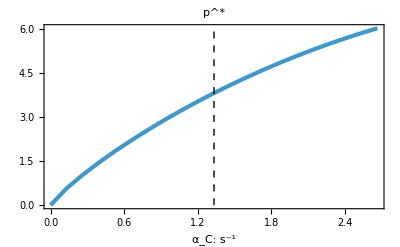
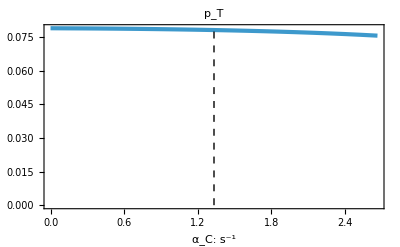
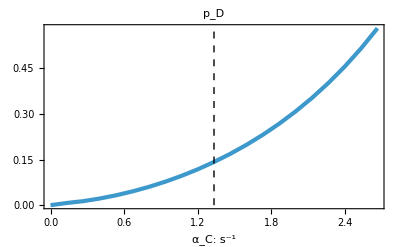
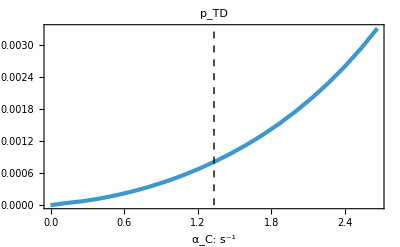
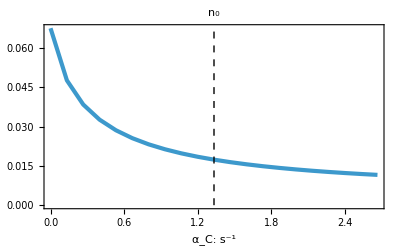
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Column[Table[(Export[NotebookDirectory[]<>figureNameSensitivity<>"/"<>figureNameSensitivity<>"_"<>(sensitivityPar/.namesUTF8)<>".pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[0],sensitivityPar,Table[i sensitivityPar/.pars[0],{i,minSensitivityRange,maxSensitivityRange,.1}],#, 24 3600,{FrameLabel->{{None,None},{Row[{sensitivityPar/.names,": ",sensitivityPar/.units}],None}},Epilog->{Black,Dashed,Line[{{sensitivityPar/.pars[4],0},{sensitivityPar/.pars[4],10^5}}]},PlotRange->Full,AxesOrigin->{Automatic,0},PlotLabel->(#/.names)}]&,quants],{sensitivityPar,sensitivityPars}]]
```